## Strategy 1

### Math

```mathematica
Clear[λ,μ]
P0[ρ_]:=(1-ρ)/(1-ρ^11) (*Stationary Distribution*)
P[ρ_,n_]:=P0[ρ]*ρ^n (*Prob of being in state n*)
PBlock[ρ_]:=P[ρ,10](*Blocking Probability*)
L[ρ_]:=∑_(n=0)^10 n*P[ρ,n](*AVG num of Customers*)
B[ρ_]:= 1-P0[ρ](*AVG num of Cust being Served*)
Lq[ρ_]:=L[ρ]-B[ρ] (*Avergae Que Length*)
S[ρ_,λ_]:=L[ρ]/λ(*AVG sojourn time*)
```

### Blocking Prob

#### Collected Data

```mathematica
PBlockS1x ={0,0.6,0.7,0.8,0.9,1.01,1.1,1.2};
PBlockS1y = ConstantArray[0,8] (*stores the blocking prob for ρ={0.1,1.2}*);
PBlockS1y[[1]]=0;
PBlockS1y[[2]]=Mean[{4/112,1/118,0,0,0,0,5/114,0,0,0}];(*ρ=0.6*)
PBlockS1y[[3]]=Mean[{5/138,0,0,1/152,0,0,1/137,0,0,3/132}];(*ρ=0.7*)
PBlockS1y[[4]]=Mean[{6/153,7/136,0,10/156,0,8/176,7/156,2/153,9/150,11/147}];(*ρ=0.8*)
PBlockS1y[[5]]=Mean[{3/199,26/185,24/158,2/173,3/169,11/185,6/182,2/171,16/183,4/174}]; (*ρ=0.9*)
PBlockS1y[[6]]=Mean[{26/190,5/173,14/175,30/194,19/186,6/188,18/191,21/176,19/179,28/189}]; (*ρ=1.01*)
PBlockS1y[[7]]=Mean[{31/207,31/195,28/204,35/185,21/189,33/187,3/219,22/190,24/188,39/191}]; (*ρ=1.1*)
PBlockS1y[[8]]=Mean[{19/206,55/215,35/194,41/217,79/204,42/204,68/199,38/204,58/188,41/182}](*ρ=1.2*);
PBlockS1Data = Transpose[{PBlockS1x,PBlockS1y}];
```

#### Plots

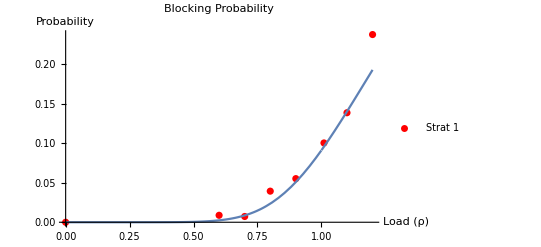

```mathematica
PBlockTherPlot = Plot[{PBlock[ρ]},{ρ,0,1.2}];

PBlockS1Plot = ListPlot[
PBlockS1Data ,
AxesLabel->{"Load (ρ)","Probability"},
PlotLabel->"Blocking Probability",
PlotStyle->Red,PlotLegends->{"Strat 1"}
];

Show[{PBlockS1Plot,PBlockTherPlot}]
```

### Avg Queue Length

#### Plots

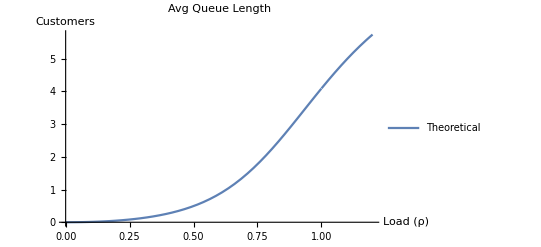

```mathematica
Plot[{Lq[ρ]},{ρ,0,1.2},AxesLabel->{"Load (ρ)","Customers"},PlotLabel->"Avg Queue Length",
PlotLegends->{"Theoretical"}]
```

### Avg Sojourn Time

#### Plots

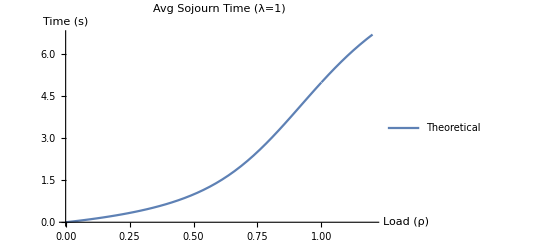

```mathematica
Plot[{S[ρ,1]},{ρ,0,1.2},AxesLabel->{"Load (ρ)","Time (s)"},PlotLabel->"Avg Sojourn Time (λ=1)",
PlotLegends->{"Theoretical"}]
```